```mathematica
H[s_]:=1/(1+2 s+2 s^2+s^3)
```

```mathematica
Simplify[H[2/π (1/z-1)/(1/z+1)] H[2/π (z-1)/(z+1)]==1/(1-64/π^6 ((z-1)/(z+1))^6)]
```

True

```mathematica
FullSimplify[(z-1)/(z+1)/.z->Exp[ⅈ w]]
```

ⅈ Tan[w/2]

```mathematica
FullSimplify[(H[2/π (1/z-1)/(1/z+1)] H[2/π (z-1)/(z+1)]/.z->Exp[ⅈ w])==1/(1-64/π^6 (ⅈ Tan[w/2])^6)]
```

True

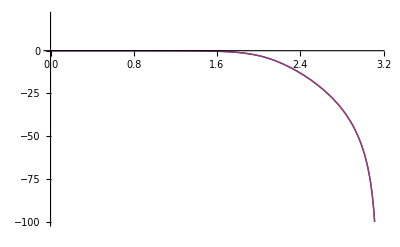

```mathematica
Plot[{
10*Log10[Abs[H[2/π (z-1)/(z+1)]/.z->Exp[ⅈ w]]^2],
10*Log10[1/(1-64/π^6 (ⅈ Tan[w/2])^6)]
},{w,0,π},PlotRange->{-100,20}]
```

```mathematica
Integrate[Log[1/(1-64/π^6 (ⅈ Tan[w/2])^6)],{w,-π,π}]
```

$Aborted

```mathematica
NIntegrate[Log[1/(1-64/π^6 (ⅈ Tan[w/2])^6)],{w,-π,π}]
```

-15.1615

```mathematica
8/π NIntegrate[Log[1/(1+1/u^6)],{u,0,π^2/4}]
```

-15.9944

```mathematica
Series[1/(1-64/π^6 (ⅈ Tan[w/2])^6),{w,π,7}]
```

(π^6 (w-π)^6)/4096+O[w-π]^8

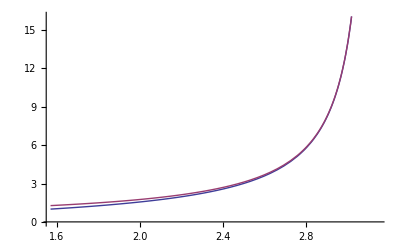

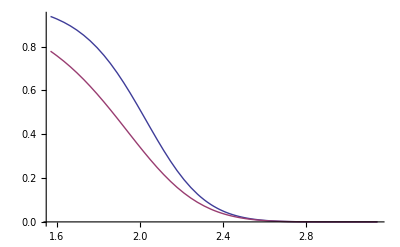

```mathematica
Plot[{Tan[w/2],(1/(π/2-w/2))},{w,π/2,π}]
Plot[{1/(1-64/π^6 (ⅈ Tan[w/2])^6),1/(1+((2/π)/(π/2-w/2))^6)},{w,π/2,π}]
```

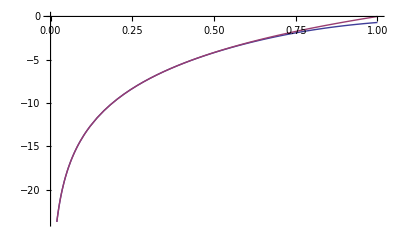

```mathematica
Plot[{Log[1/(1+1/u^6)],Log[u^6]},{u,0,1}]
```

```mathematica
Integrate[Log[u^6],u]
```

-6 u+u Log[u^6]

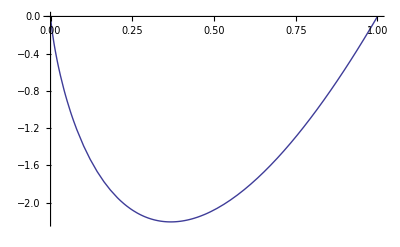

```mathematica
Plot[u Log[u^6],{u,0,1}]
```

```mathematica
Limit[-6 u+u Log[u^6],u->0]
```

0